## Pulsar analysis

```mathematica
Get@"init.m"
""
""
(*These first Four won't work (everywhere?) for some reason, but I can use traditional form anyway. *)
(*Notation[∂f_[x_]/∂x_ ⟸ D[f_,x_]]
Notation[∂^n_ f_[x_]/∂x_^n_ ⟸ D[f_,{x_,n_}]]

Notation[ⅆf_[x_]/ⅆx_ ⟸ Dt[f_][x_]]
Notation[ⅆ^n_ f_[x_]/ⅆ x_^n_ ⟸ Dt[f_][{x_,n_}]]*)

Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]


Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]
"Notations"
"Notations"
Notation[∂/(∂x_) f_  ⟹ D[f_,x_]]
Notation[(∂f_)/(∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_)/(∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[∂^n_/(∂x_^n_) f_ ⟹ D[f_,{x_,n_}]]

(* Mixed partials *)
Notation[(∂^2 f_)/(∂x_∂y_) ⟹ D[f_,x_,y_]]

Notation[∂^2/(∂x_∂y_)f_ ⟹ D[f_,x_,y_]]
(* Next two currently don't work *)
(*Notation[(∂^(n_+m_) f_)/(∂x_^n_∂y_^m_) ⟹ D[f_,{x_,n_},{y_,m_}]]
Notation[∂^(n_+m_)/(∂x_^n_∂y_^m_) f_ ⟹ D[f_,{x_,n_},{y_,m_}]]*)
"Fixed notation"
"Fixed notation"
SetOptions[Plot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ListPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ContourPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ParametricPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ReImPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[VectorPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[DensityPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ComplexPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[Plot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotLabels->Automatic,PlotRange->All];
SetOptions[ListPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ContourPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[VectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[SliceVectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[DensityPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ComplexPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotRange->All];
"plotting options"
"plotting options"
SetOptions[Manipulate,Paneled->False];
"more options"
"more options"
```

Notations

Notations

Fixed notation

Fixed notation

plotting options

plotting options

more options

more options

WolframAlphaQueryParseResults

-Graphics-

```mathematica
1/ 1. 3373
```

3373.

```mathematica
10^51
```

1000000000000000000000000000000000000000000000000000

WolframAlphaQueryParseResults

Sat 29 Jan 2022

-Graphics-

```mathematica
TeXForm[-11/(-3(x^2)^(1/10))]
```

\frac{11}{3 \sqrt[10]{x^2}}

```mathematica
D[(1/f), f]
```

-1/f^2

```mathematica
p=1/f
```

1/f

```mathematica
Δf=10^-3
```

1/1000

```mathematica
ClearAll@Δf
```

```mathematica
Δp=√((D[(1/f), f] Δf)^2)
%//PowerExpand
```

√(Δf^2/f^4)

Δf/f^2

-Graphics-

```mathematica
μ=2
```

2

```mathematica
σ=√(1/M((1-μ)^2+(3-μ)^2))/.M->2
```

1

```mathematica
σ/μ^2
```

1/4

```mathematica
6.8 * 10 - 7.662 * 10^-3
```

67.9923

-Graphics-

```mathematica
6.8 10^1-7+1.662 10^-3
```

61.0017

### Calculations on the quantities

```mathematica
c=LinguisticAssistant;
p0=wa["76 * 10^-7 +1.662*10^-3 seconds"]
p0::usage="This is the period at the equilibrium line of the sine wave.";
p=wa["83*10^-7 + 1.662*10^-3 seconds"]
p::usage="This is the period of the sine wave at the highest amplitude";
```

0.0016696 s

0.0016703 s

```mathematica
(*vs=c(p0/p-1)//UnitConvert[#,"Kilometers"/"Seconds"]&*)
```

We retrieve the correct order of magnitude vs from python

```mathematica
vs=LinguisticAssistant
```

13.3 km/s

```mathematica
T=wa["0.48 - 0.32 days"]
T::usage="The period corresponding to the orbit of the pulsar around the center of mass. It is calculated using the period of the sine wave.";
```

0.16 days

```mathematica
T//UnitConvert[#,"Hours"]&
```

3.84 h

```mathematica
r=(Abs@vs T)/(2π)
```

29262.1 km

```mathematica
r/LinguisticAssistant
```

0.0806849

WRONG calculation of Mc, we use the mass function below.

```mathematica
T^2/r^3==(4 π^2)/(G(MP+MC))//Solve[#,MC]&
```

{{MC→(-G T^2 MP+4 r^3 π^2)/(G T^2)}}

```mathematica
G=LinguisticAssistant//UnitConvert
Mp=LinguisticAssistant;
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Mc=(-G T^2 Mp+4 r^3 π^2)/(G T^2)
```

-2.98252×10^30 kg

```mathematica
Mc/LinguisticAssistant
```

-1.49993

if the mass of the companion is sufficiently big, we approximate F = F_c, then

NOTE: It is not, thus this is a bad approximation, go to the mass function below.

```mathematica
v=Abs@vs
```

13.3 km/s

```mathematica
Mc=(v^2 r)/G
```

7.75538×10^25 kg

```mathematica
Mc/LinguisticAssistant
```

0.0000390024

Verifying the modified julian date

```mathematica
LinguisticAssistant
```

Year: 2012

```mathematica
v/LinguisticAssistant
```

0.446569

```mathematica
v/LinguisticAssistant
```

0.280816

#### More quantities

```mathematica
ρ==M/(4/3 π R^3)//Solve[#,R]&
```

{{R→-(M^(1/3) (-3/π)^(1/3))/(2^(2/3) ρ^(1/3))},{R→(M^(1/3) (3/π)^(1/3))/(2^(2/3) ρ^(1/3))},{R→((-1)^(2/3) M^(1/3) (3/π)^(1/3))/(2^(2/3) ρ^(1/3))}}

Assume the density of the sun

```mathematica
R=R/.%[[2]][[1]]/.{M->Mc,ρ->LinguisticAssistant}//UnitConvert
```

2.36032×10^7 m

```mathematica
R/LinguisticAssistant
```

0.0339272

```mathematica
R/LinguisticAssistant
```

0.0650815

#### Mass function

It gives a lower bound for the mass of the companion star.

-Graphics-

```mathematica
Solve[m2^3/(m1+m2)^2==P/(2π G)K1^3,m2]//First
```

{m2→(K1^3 P)/(6 G π)-(-K1^6 P^2-12 G K1^3 m1 P π)/(6 G π (K1^9 P^3+18 G K1^6 m1 P^2 π+54 G^2 K1^3 m1^2 P π^2+6 √3 π^(3/2) √(2 G^3 K1^9 m1^3 P^3+27 G^4 K1^6 m1^4 P^2 π))^(1/3))+((K1^9 P^3+18 G K1^6 m1 P^2 π+54 G^2 K1^3 m1^2 P π^2+6 √3 π^(3/2) √(2 G^3 K1^9 m1^3 P^3+27 G^4 K1^6 m1^4 P^2 π))^(1/3))/(6 G π)}

```mathematica
McMinimal/Mp
```

McMinimal (0.666667 /M_☉)

```mathematica
McMinimal/LinguisticAssistant
```

McMinimal (1 /M_☉)

```mathematica
LinguisticAssistant/LinguisticAssistant
```

333000.

The ratio of the companion star to the pulsar is much smaller than the ratio of the sun to the earth; is it reasonable to assume that the pulsar orbits around the companion (situation 2)? A: It is not, and we ignore this idea all together.

#### Conservation of angular momentum

Can we use conservation of angular momentum to determine r_1 and r_2?

ℓ = | r×p | = r m v sin θ

```mathematica
ω==2π f
```

ω==2 f π

#### Doing calculations again on minimal distance

-Graphics-

-Graphics-

```mathematica
rCubed=x/.First[T^2/x==(4 π^2)/(G M)//Solve[#,x]&]
```

(G M T^2)/(4 π^2)

```mathematica
r=First[rCubed^(1/3)/.{T->T,M->{Mp+McMinimal},G->G}//UnitConvert[#,"Kilometers"]&]
```

UnitConvert[(((0.0127548 m^3/kg) (McMinimal+1.5 M_☉))^(1/3))/(2 π)^(2/3),Kilometers]

```mathematica
r/LinguisticAssistant
```

(2.75732×10^-6 /km) UnitConvert[(((0.0127548 m^3/kg) (McMinimal+1.5 M_☉))^(1/3))/(2 π)^(2/3),Kilometers]

-Graphics-

```mathematica
??T
```

### Try to fit in MMA

Get list of x and y values from python

```mathematica
x ={56300.4688155539,56300.45492639893,56300.44103724313,56300.42714808649,56300.413258929024,56300.39936977075,56300.38548061164,56300.37159145176,56300.35770229113,56300.34381312978};
y ={0.0016627957592090326,0.00166282563896264,0.0016628302415629193,0.0016628131097909669,0.0016627781654799023,0.0016627323139534107,0.0016626925155149316,0.0016626750457100386,0.0016626881480292916,0.001662710837899844};
err={2.353097663263867*10^(-9),2.3435228659575588*10^(-9),2.2291472249414805*10^(-9),1.9880488969239098*10^(-9),3.1889485827440945*10^(-9),3.46808484243367*10^(-9),2.1726783415015955*10^(-9),5*10^(-9),2.2821954279209845*10^(-9),3.615634992325844*10^(-9)};

data=Transpose[{x,y}];
```

```mathematica
FindFit[y ,B+A Sin[ω x + ϕ],{B, A, ω, ϕ},x]
```

{B→0.00166275,A→-7.81285×10^-8,ω→0.574299,ϕ→3.12734}

This one comes from python

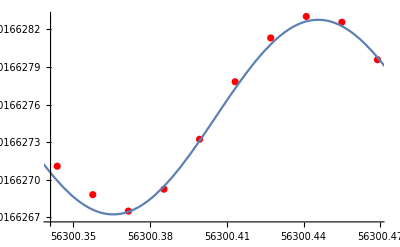

```mathematica
Show[
ListPlot[data,PlotStyle->Red]
,Plot[B+A Sin[ω x + ϕ]/.{B->0.00166275,A ->7.7591 10^-8,ω->2π * 6.25007714, ϕ->-24.3685230},{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

We’ll now attempt to fit better using MMA, and using our found values from python as initial values.

#### No weights

```mathematica
nlm=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 6.25007714},{ϕ,-24.3685230}},x]
```

FittedModel[0.00166275-7.81285×10^-8 Sin[117036.-41.3487 x]]

```mathematica
nlm["BestFit"]
```

0.00166275-7.81285×10^-8 Sin[117036.-41.3487 x]

```mathematica
yWithErr=MapThread[Around,{y,err}]
```

{0.001662795824,0.001662825623,0.001662830222,0.001662813120,0.001662778232,0.001662732335,0.001662692522,0.0016626755,0.001662688123,0.0016627114}

```mathematica
dataWithErr=Transpose[{x,yWithErr}]
```

{{56300.5,0.001662795824},{56300.5,0.001662825623},{56300.4,0.001662830222},{56300.4,0.001662813120},{56300.4,0.001662778232},{56300.4,0.001662732335},{56300.4,0.001662692522},{56300.4,0.0016626755},{56300.4,0.001662688123},{56300.3,0.0016627114}}

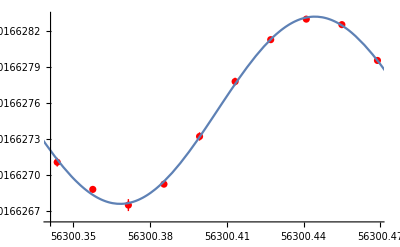

```mathematica
Show[
ListPlot[dataWithErr,PlotStyle->Red]
,Plot[nlm["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

{5.6886×10^-11,6.36044×10^-10,-1.34404×10^-9,-2.28501×10^-10,2.04978×10^-9,4.53148×10^-10,-2.25744×10^-9,-1.7062×10^-9,4.56825×10^-9,-2.22794×10^-9}

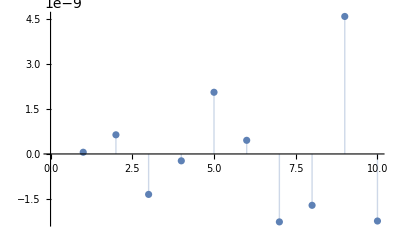

```mathematica
nlm["FitResiduals"]
ListPlot[%,Filling->Axis]
```

```mathematica
nlm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableMeanSquares,ANOVATableSumsOfSquares,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,EstimatedVariance,FitCurvatureTable,FitCurvatureTableEntries,FitResiduals,Function,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterBias,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals}

```mathematica
Style[nlm["ANOVATable"],Background->White]
```

| DF | SS | MS
Model | 4 | 0.0000276475 | 6.91188×10^-6
Error | 6 | 4.05131×10^-17 | 6.75219×10^-18
Uncorrected Total | 10 | 0.0000276475 | 
Corrected Total | 9 | 3.34502×10^-14 |

```mathematica
Style[nlm["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 8.29897×10^-10 | 2.00357×10^6 | 1.04347×10^-36
A | 7.81285×10^-8 | 1.1668×10^-9 | 66.9594 | 7.46294×10^-10
ω | 41.3487 | 0.418112 | 98.8939 | 7.20421×10^-11
ϕ | -117036. | 23539.9 | -4.9718 | 0.0025223

#### Using weights err

```mathematica
nlmWeightsErr=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 6.25007714},{ϕ,-24.3685230}},x,Weights->err]
```

FittedModel[0.00166275-7.84907×10^-8 Sin[115563.-41.3226 x]]

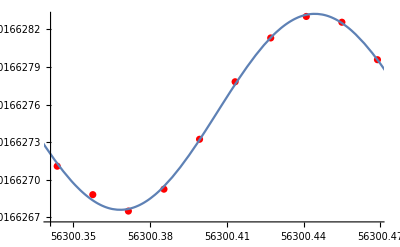

```mathematica
Show[
ListPlot[data,PlotStyle->Red]
,Plot[nlm["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

```mathematica
Style[nlmWeightsErr["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 8.0565×10^-10 | 2.06387×10^6 | 8.73404×10^-37
A | 7.84907×10^-8 | 1.12952×10^-9 | 69.4906 | 5.97492×10^-10
ω | 41.3226 | 0.399323 | 103.481 | 5.48896×10^-11
ϕ | -115563. | 22482.1 | -5.14023 | 0.00213554

```mathematica
Style[nlmWeightsErr["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
B | 0.00166275 | 8.0565×10^-10 | {0.00166275,0.00166276}
A | 7.84907×10^-8 | 1.12952×10^-9 | {7.57269×10^-8,8.12545×10^-8}
ω | 41.3226 | 0.399323 | {40.3455,42.2997}
ϕ | -115563. | 22482.1 | {-170575.,-60551.3}

#### Using weights 1 / err

```mathematica
nlmWeightsOneOverErr=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 6.25007714},{ϕ,-24.3685230}},x,Weights->1/err]
```

FittedModel[0.00166275-7.78642×10^-8 Sin[121239.-41.4234 x]]

```mathematica
nlm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableMeanSquares,ANOVATableSumsOfSquares,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,EstimatedVariance,FitCurvatureTable,FitCurvatureTableEntries,FitResiduals,Function,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterBias,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals}

```mathematica
Style[nlm["ANOVATable"],Background->White]
```

| DF | SS | MS
Model | 4 | 0.0000276475 | 6.91188×10^-6
Error | 6 | 4.05131×10^-17 | 6.75219×10^-18
Uncorrected Total | 10 | 0.0000276475 | 
Corrected Total | 9 | 3.34502×10^-14 |

```mathematica
Show[
ListPlot[data,PlotStyle->Red]
,Plot[nlm["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

-Graphics-

```mathematica
Style[nlmWeightsOneOverErr["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 8.3382×10^-10 | 1.99414×10^6 | 1.07342×10^-36
A | 7.78642×10^-8 | 1.14757×10^-9 | 67.8516 | 6.8938×10^-10
ω | 41.4234 | 0.425049 | 97.4557 | 7.86576×10^-11
ϕ | -121239. | 23930.4 | -5.06633 | 0.00229629

```mathematica
Style[nlmWeightsOneOverErr["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
B | 0.00166275 | 8.3382×10^-10 | {0.00166275,0.00166276}
A | 7.78642×10^-8 | 1.14757×10^-9 | {7.50562×10^-8,8.06722×10^-8}
ω | 41.4234 | 0.425049 | {40.3833,42.4635}
ϕ | -121239. | 23930.4 | {-179795.,-62683.7}

### Repeating the analysis with fit results

```mathematica
nlm["BestFitParameters"]
nlmWeightsErr["BestFitParameters"]
nlmWeightsOneOverErr["BestFitParameters"]
```

{B→0.00166275,A→7.81285×10^-8,ω→41.3487,ϕ→-117036.}

{B→0.00166275,A→7.84907×10^-8,ω→41.3226,ϕ→-115563.}

{B→0.00166275,A→7.78642×10^-8,ω→41.4234,ϕ→-121239.}

```mathematica
nlm["ParameterTable"]//InputForm
```

Style[Grid[{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, 
   {B, 0.001662754198233496, 8.298972930483922*^-10, 2.0035662390533176*^6, 1.043473784522389*^-36}, 
   {A, 7.812852992237989*^-8, 1.1668045838974702*^-9, 66.95939577251886, 7.462940980943583*^-10}, 
   {ω, 41.348728532499294, 0.4181118431676514, 98.89394239406796, 7.20421126600517*^-11}, 
   {ϕ, -117035.54024413231, 23539.866620113626, -4.971801333153322, 0.0025223029865294017}}, 
  Alignment -> {Left, Automatic}, Dividers -> {{2 -> GrayLevel[0.7]}, {2 -> GrayLevel[0.7]}}, 
  Spacings -> {{2 -> 1}, {2 -> 0.75}}], "DialogStyle"]

```mathematica
δB=8.298972930483922*^-10 LinguisticAssistant;
δA=1.1668045838974702*^-9 LinguisticAssistant;
δω=0.4181118431676514 LinguisticAssistant;
δϕ=23539.866620113626;
```

```mathematica
{B,A,ω,ϕ}={B LinguisticAssistant,A LinguisticAssistant,ω LinguisticAssistant,ϕ}/.nlm["BestFitParameters"]
```

{0.00166275 s,7.81285×10^-8 s,41.3487 per day,-117036.}

```mathematica
B+A Sin[ω t+ϕ];
```

```mathematica
f=2π Around[ω,δω]
```

(259.82.6) per day

```mathematica
c=LinguisticAssistant;
p=Around[B,δB]+Around[A,δA]
p::usage="This is the period of the sine wave at the highest amplitude";
p0=Around[B,δB]
p0::usage="This is the period at the equilibrium line of the sine wave.";
i(* assumption *)=90°; 
Mp (* assumption *)=LinguisticAssistant ;
```

(0.001662832314) s

(0.00166275428) s

```mathematica
Quantity[(0.001662832314), "Seconds"]//InputForm
```

Quantity[Around[0.0016628323267634183, 1.4318388366059908*^-9], "Seconds"]

```mathematica
vs=c(p0/p-1)//UnitConvert[#,"Kilometers"/"Seconds"]&;
v=Abs@vs
```

(14.090.30) km/s

```mathematica
T=2π/Around[ω,δω] //UnitConvert[#,"Hours"]&
T::usage="The period corresponding to the orbit of the pulsar around the center of mass. It is calculated using the period of the sine wave.";
```

(3.650.04) h

```mathematica
ap=(v T)/(2π) (* from v=(2πr)/T *)
ap/LinguisticAssistant
```

(29433.691.) km

0.08120.0019

```mathematica
Solve[m2^3/(m1+m2)^2==T/(2π G)K1^3,m2]; 
McMin=m2/.First[%/.{m1->Mp,T->T,G->G,K1->Sin[i]v}]
(McMin /LinguisticAssistant )LinguisticAssistant 
McMin/Mp
```

8.970.1310^28 kg

(0.04510.0007) M_☉

0.03220.0005

#### Kepler to determine acMin

```mathematica
Solve[T^2/a^3==(4 π^2)/(G(McMin+Mp)),a]//First
a=a/.%/.{G->G,T->T,McMin->McMin,Mp->Mp}//UnitConvert[#,"Kilometers"]&
```

{a→(G^(1/3) T^(2/3) (McMin+Mp)^(1/3))/(2 π)^(2/3)}

9.430.0610^5 km

```mathematica
acMin=a-ap//UnitConvert[#,"Kilometers"]&
```

9.130.0610^5 km

```mathematica
19/3//N
```

6.33333

```mathematica
LinguisticAssistant//UnitConvert//N
```

6.62607×10^-34 kg m^2/s

```mathematica
LinguisticAssistant//UnitConvert//N
```

9.10938×10^-31 kg

#### Mass for various inclinations i

```mathematica
ClearAll[i]
```

```mathematica
sol=First@Solve[m2^3/(m1+m2)^2 Sin[i]^3==T/(2π G)K1^3,m2];
```

```mathematica
Solve[a x^3+b x^2+c x+d==0,x]//First; (* cubic formula *)
```

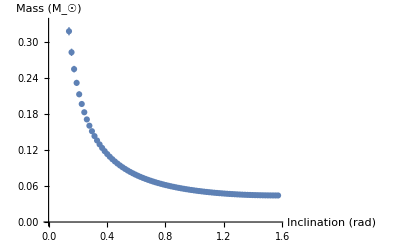

```mathematica
sol=Solve[m2^3/(m1^2(* assuming m1 >> m2 *))Sin[i]^3==T/(2π G)K1^3,m2][[2]];
step=1°;
masses=Table[m2/.sol/.{m1->Mp,T->T,G->G,K1->(*Sin[i]*)Abs[c(p0/p-1) ](*v*)},{i,step,90°,step}];
massesMag=QuantityMagnitude[UnitConvert[masses]];
inclinations=Table[i,{i,step,90°,step}];
massData=Transpose[{inclinations,massesMag / LinguisticAssistant}];
ListPlot[massData,AxesLabel->{"Inclination (rad)","Mass (M_☉)"},TicksStyle->Black,Background->White,AxesStyle->Black]
```

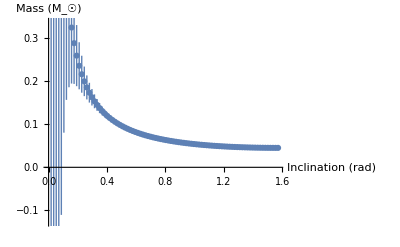

```mathematica
sol=Solve[m2^3/(m1+m2)^2 Sin[i]^3==T/(2π G)K1^3,m2][[1]];
step=1°;
masses=Table[m2/.sol/.{m1->Mp,T->T,G->G,K1->(*Sin[i]*)Abs[c(p0/p-1) ](*v*)},{i,step,90°,step}];
massesMag=QuantityMagnitude[UnitConvert[masses]];
inclinations=Table[i,{i,step,90°,step}];
massData=Transpose[{inclinations,massesMag / LinguisticAssistant}];
ListPlot[massData,AxesLabel->{"Inclination (rad)","Mass (M_☉)"},TicksStyle->Black,Background->White,AxesStyle->Black]
```